```mathematica
Clear["Global`*"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<"Sampler1`";
```

```mathematica
U[x_,y_]=100/2(√(x^2+y^2)-10)^2;
dU[x_,y_]=GradientG[U[x,y],{x,y}];
ddU[x_,y_]=HessianH[U[x,y],{x,y}];
```

1001 -36611.2 13.328 0.472934 0.475955 36911.2 300 300 0.0000139124 0.000014192 True {1,11} {1,4,11}

2002 151.282 1.10032 0.979426 0.0263306 148.862 300.282 300.144 0.000873158 0.00124929 False {1,11} {1,11}

3003 300.128 9.14305 0.694912 0.392196 7.26621 307.395 382.151 0.00170069 0.00913981 True {1,3,9,11} {1,11}

4004 418.243 -1.4367 0.671789 0.353249 5.59932 309.501 423.843 0.00236173 0.0167703 False {1,2,9,11} {1,3,11}

5005 301.831 10.6504 0.549518 0.429088 8.27122 310.102 428.477 0.00279701 0.0208743 True {1,4,5,7,11} {1,11}

6006 423.116 -8.14817 0.705258 0.430671 5.36113 310.102 428.477 0.00279701 0.0208743 False {1,2,4,11} {1,3,5,11}

7007 306.064 11.3413 0.604602 0.412232 4.03841 310.102 428.477 0.00279701 0.0208743 True {1,4,8,9,11} {1,11}

8008 417.738 1.23152 0.523723 0.399179 10.7395 310.102 428.477 0.00279701 0.0208743 False {1,2,4,11} {1,3,11}

9009 305.801 19.8611 0.664489 0.415746 4.30119 310.102 428.477 0.00279701 0.0208743 True {1,6,9,11} {1,5,11}

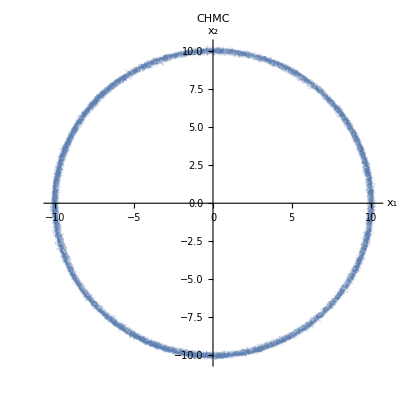

```mathematica
QS=hmc[U,dU,ddU,2,5000,10000,True,True];
ListPlot[QS,AspectRatio->1,PlotStyle->Opacity[0.1],AxesLabel->{"x_1","x_2"},PlotStyle->{Green},PlotLabel->CHMC]
```

1001 53.1593 10.3073 0.911015 0.123311 246.952 300.111 300 0.000798363 1.×10^-7 True {1,11} {1,8,11}

2002 307.531 8.23228 0.836614 0.283882 3.18469 310.716 300 0.00211687 1.×10^-7 True {1,2,7,9,11} {1,11}

3003 305.79 10.5864 0.760014 0.358068 5.53915 311.329 300 0.0024092 1.×10^-7 True {1,2,5,7,11} {1,11}

4004 307.07 13.3422 0.680626 0.378511 4.87355 311.943 300 0.00263491 1.×10^-7 True {1,2,3,10,11} {1,11}

5005 304.894 11.6043 0.70428 0.411252 7.66675 312.561 300 0.00271475 1.×10^-7 True {1,2,8,11} {1,11}

6006 309.381 8.1029 0.47087 0.294806 3.17932 312.561 300 0.00271475 1.×10^-7 True {1,3,5} {11}

7007 308.817 8.95064 0.373966 0.390611 3.74344 312.561 300 0.00271475 1.×10^-7 True {1,2,6} {1,11}

8008 307.722 5.28629 0.486386 0.439044 4.83817 312.561 300 0.00271475 1.×10^-7 True {1,6,8,11} {1,11}

9009 305.332 6.2574 0.557772 0.385492 7.22892 312.561 300 0.00271475 1.×10^-7 True {1,3,5,7,11} {1,11}

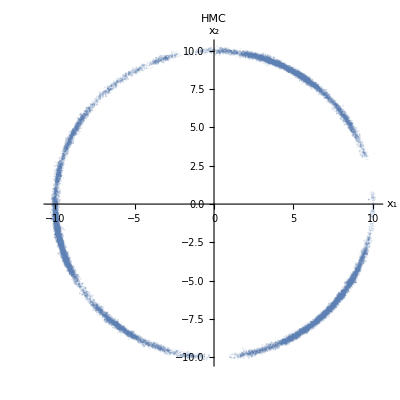

```mathematica
QS=hmc[U,dU,ddU,2,5000,10000,True,False];
ListPlot[QS,AspectRatio->1,PlotStyle->Opacity[0.1],AxesLabel->{"x_1","x_2"},PlotStyle->{Green},PlotLabel->HMC]
```

1001 -7.26295 5.21508 0.930147 0.129568 307.263 300 300 1.×10^-7 0.00186002 False {1,11} {1,11}

2002 313.118 50.5758 0.743984 0.32255 11.1087 300 324.227 1.×10^-7 0.0310789 False {1,2,9,11} {1,11}

3003 312.092 22.7492 0.368347 0.441566 12.1352 300 324.227 1.×10^-7 0.0449114 False {1,2,7,8,11} {1,11}

4004 309.472 72.5163 0.352261 0.368867 14.1258 300 323.598 1.×10^-7 0.0423086 False {1,11} {1,11}

5005 315.026 70.9092 0.512896 0.416017 8.26134 300 323.287 1.×10^-7 0.0449114 False {1,2,7,10,11} {1,11}

6006 305.795 24.556 0.378689 0.448738 17.4922 300 323.287 1.×10^-7 0.0449114 False {1,4,7,10,11} {1,11}

7007 308.442 32.4567 0.297975 0.312896 14.8454 300 323.287 1.×10^-7 0.0449114 False {1,8} {1,11}

8008 311.887 92.7516 0.766638 0.395646 11.4003 300 323.287 1.×10^-7 0.0449114 False {1,6,7,9,10,11} {1,11}

9009 317.649 68.3346 0.403037 0.356048 5.63851 300 323.287 1.×10^-7 0.0449114 False {1,2,5,10} {1,2,11}

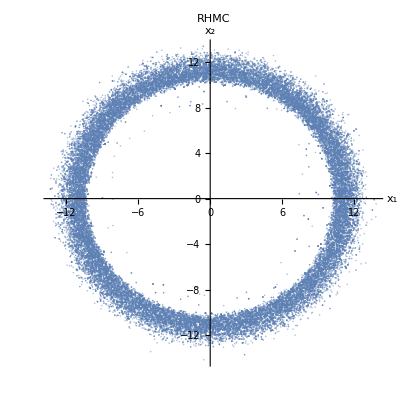

```mathematica
U[x_,y_]=1/2(√(x^2+y^2)-10)^2;
dU[x_,y_]=GradientG[U[x,y],{x,y}];
ddU[x_,y_]=HessianH[U[x,y],{x,y}];
QS=hmc[U,dU,ddU,2,5000,10000,False,False];
ListPlot[QS,AspectRatio->1,PlotStyle->Opacity[0.5],AxesLabel->{"x_1","x_2"},PlotStyle->{Green},PlotLabel->RHMC]
```